# The sum of Lagrange numbers

```mathematica
SetDirectory[NotebookDirectory[]];
markovNums = ReadList["Markov153665.txt"];
S = 4-GoldenRatio-√2;
c=0.18071710471180647805779264904916762147630562767088273^(-.5);
```

```mathematica
Block[{$MaxExtraPrecision=1000},
Reinitialize = False;
incMax = 20;

Print["Reading files..."];
CopyFile["remaindersF.txt","remaindersF.backup.txt", OverwriteTarget->True];
CopyFile["remaindersN.txt","remaindersN.backup.txt", OverwriteTarget->True];
While[Reinitialize,
 Print["Reinitialization! Clearing files..."];DeleteFile["remaindersF.txt"];CreateFile["remaindersF.txt"];DeleteFile["remaindersN.txt"];CreateFile["remaindersN.txt"]; Reinitialize = False];
RFdata=ReadList["remaindersF.txt"];
Ninit = If[Length[RFdata]==0,0, RFdata[[1]]];
RFinit =If[Ninit==0,S, RFdata[[2]]];
check =Ninit==Length[ReadList["remaindersN.txt"]];
If[!(check),
 Print["Bad initialization!"];DeleteFile["remaindersF.txt"];CreateFile["remaindersF.txt"];DeleteFile["remaindersN.txt"];CreateFile["remaindersN.txt"];
 Ninit=0; RFinit = S; RNlength=0;RNinit = N[S,10];];
RF = RFinit;
n = Ninit+1;
Print["Computation time (in seconds): ",Timing[
While[n≤Ninit+incMax,
If[Mod[n,5]==0 , NotebookDelete[temp]; temp=PrintTemporary["Computing n = ", n, "..."]; ];
RF-= 3-√(9-4/markovNums[[n]]^2);N[RF,10]>>>"remaindersN.txt";
n++;]][[1]]];
Print["Writing files..."];
Export["remaindersF.txt",{n-1, RF}];
CopyFile["remaindersF.txt","remaindersF"<>ToString[n-1]<> ".txt"];
CopyFile["remaindersN.txt","remaindersN"<>ToString[n-1]<> ".txt"];
Print["Last index computed: n = ",n-1];
Print["Last remainder computed: R_n = ",N[RF,10]];
]
```

Reading files...

Computation time (in seconds): 18.0515

Writing files...

Last index computed: n = 21250

Last remainder computed: R_n = 5.32107443×10^-296

```mathematica
remaindersN = ReadList["remaindersN.txt"];
M=Length[remaindersN];
M = 20000;
expectedR[n_] := (6 √n)/c ⅇ^(-2c √n);
expected = Table[N[expectedR[n],10],{n,1,M}];
```

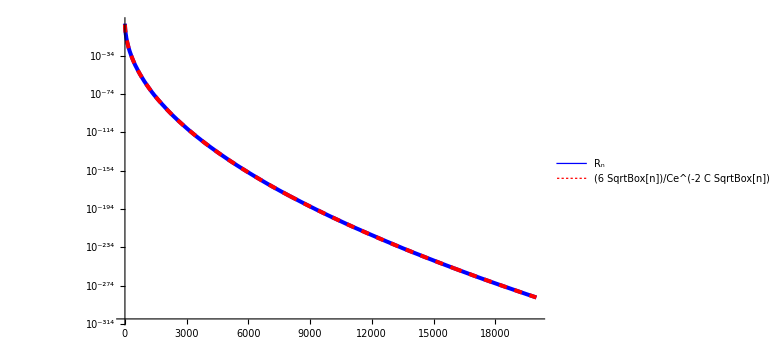

```mathematica
ListLogPlot[{remaindersN[[1;;M]],expected[[1;;M]]},Joined->True,PlotStyle->{{Joined,Blue, Thickness[0.005]},{Dashing[0.01],Red,  Thickness[0.005]}},PlotLegends->{"R_n","(6 SqrtBox[n])/Ce^(-2 C SqrtBox[n])"}, Ticks->{Automatic, Automatic},TicksStyle->15,  ImageSize->Large]
```

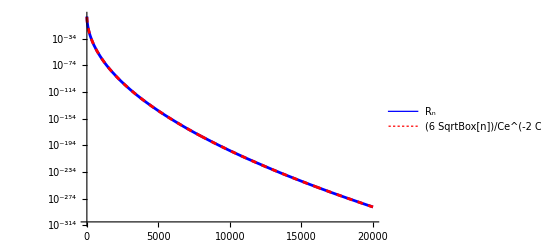

```mathematica
ListLogPlot[{remaindersN[[1;;M]],expected[[1;;M]]},Joined->True,PlotStyle->{{Joined,Blue, Thickness[0.005]},{Dashing[0.01],Red,  Thickness[0.005]}},PlotLegends->{"R_n","(6 SqrtBox[n])/Ce^(-2 C SqrtBox[n])"}, Ticks->{Automatic, {{1,1}, {10^-100,"10^-100"}, {10^-200,"10^-200"}}}, TicksStyle->60,  AxesStyle->Thick, ImageSize->Full]
```